# Wolfram语言专题讲座 机器学习和人工智能

杨圣汇 Wolfram Research Inc

-Graphics-

## 提纲

### 监督学习-预测回归/Regression

适用于使用回归来解决的问题

Predict: Wolfram语言中内置的预测和回归函数

示例：仪表板读数预测

示例：预测油耗 MPG = Miles per Gallon

其他输入数据类型

定制 Predict 预测函数：算法选项

定制 Predict 预测函数：性能目标

### 序列预测

SequencePredict: Wolfram语言中内置的预测和回归函数

示例：莎士比亚诗词

### 进阶内容

不平衡的数据

不平衡的预测输出

## 适用于使用Predict来解决的问题

一般来讲回归模型通过特征值输入（例如房屋面积，卧室数量，离市中心的距离等等）来预测连续数值结果（例如房价）。输出结果可以表达

多少价格

合理定价范围

运动员场上表现

发电站的预期收益

网站的链接的点击量

指定区域的共享单车投放数量

等等

## Predict: Wolfram语言中内置的预测和回归函数

我们随机产生一组训练数据。数据由数值特征/numeric feature 和目标输出/target

```mathematica
trainingset = {1->1.3,2->2.4,3->6.4,4->10.1};
```

训练预测器

```mathematica
p=Predict[trainingset]
```

PredictorFunction[…]

在测试样本上测试预测器，根据分布和实用功能获得最佳预测：

```mathematica
p[1.5]
```

2.01766

询问基于输入特征值的预测目标值的分布

```mathematica
dist=p[1.5,"Distribution"]
```

NormalDistribution[2.01766,1.05357]

绘制预测值分布的概率密度函数

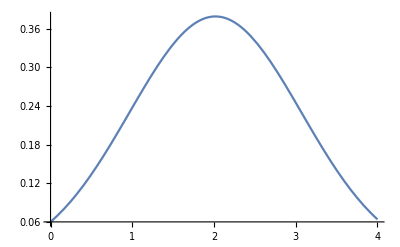

```mathematica
Plot[PDF[dist,x],{x,0,4}]
```

## 示例：仪表板读数预测

设置仪表读数图像培训数据集

```mathematica
trainingset=Image[AngularGauge[#]]->#&/@RandomReal[1,100];
```

选取三个元素

```mathematica
RandomSample[trainingset,3]
```

{-Graphics-→0.424839,-Graphics-→0.202278,-Graphics-→0.696194}

基于图像训练预测器

```mathematica
predictor=Predict[trainingset]
```

PredictorFunction[…]

产生一张测试图片

```mathematica
Image[AngularGauge[RandomReal[]]]
```

-Graphics-

预测仪表板读数

```mathematica
predictor[%]
```

0.497817

用以上结果可视化仪表板

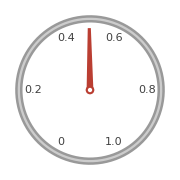

```mathematica
AngularGauge[%]
```

设置一个动态窗口，比较真实结果和训练过的预测器函数的相应输出

```mathematica
Row[{
AngularGauge[Dynamic[t]],
Style["→", Large],
Dynamic[Labeled[AngularGauge[predictor[Image[AngularGauge[t]]]],"(:9884:6d4b:7ed3:679c)"]]},BaseStyle->FontFamily->"Sans Serif"]
```

→

## 示例：预测油耗 MPG = Miles per Gallon

数据来源: UCI Machine Learning Repository Auto MPG Data Set

“The data concerns city-cycle fuel consumption in miles per gallon, to be predicted in terms of 3 multivalued discrete and 5 continuous attributes.” -Quinlan, 1993

### 自动预测

从网站导入数据

```mathematica
autoMPGData = Import["https://archive.ics.uci.edu/ml/machine-learning-databases/auto-mpg/auto-mpg.data","Data"];
```

随机找出若干行数据

```mathematica
RandomSample[autoMPGData,5]
```

{{27.0   4   101.0      83.00      2202.      15.3   76  2,renault 12tl},{34.5   4   100.0      ?          2320.      15.8   81  2,renault 18i},{14.0   8   318.0      150.0      4237.      14.5   73  1,plymouth fury gran sedan},{13.0   8   307.0      130.0      4098.      14.0   72  1,chevrolet chevelle concours (sw)},{15.0   8   383.0      170.0      3563.      10.0   70  1,dodge challenger se}}

每一行的函数头是列表

```mathematica
autoMPGData[[1]]//Head
```

List

每一行当中的元素的类型

```mathematica
Head/@autoMPGData[[1]]
```

{String,String}

需要把第一个字符串类型转化成一个数组

```mathematica
autoMPGData[[1]][[1]]
```

18.0   8   307.0      130.0      3504.      12.0   70  1

简单数据清洗

```mathematica
"1.2"+1
```

1+1.2

```mathematica
StringSplit["1 2 3"]
```

{1,2,3}

```mathematica
Flatten[{{1,2,3},"name"}]
```

{1,2,3,name}

```mathematica
ToExpression["?"]
```

Information::basic: ?Name gives information on Name, ?Ab* on all symbols starting with Ab. ??Name gives more information.

```mathematica
cleanData =Flatten[{If[#==="?",Null,ToExpression[#]]&/@StringSplit[#[[1]]],#[[2]]}]&/@ autoMPGData;
```

用 Missing 处理缺失数据

```mathematica
cleanData = cleanData /. Null-> Missing[];
```

检查样本数量

```mathematica
autoMPGData//Length
```

398

```mathematica
cleanData//Length
```

398

```mathematica
cleanData//Dimensions
```

{398,9}

把数据分为训练集和测试集

```mathematica
cleanData[[1]]
```

{18.,8,307.,130.,3504.,12.,70,1,chevrolet chevelle malibu}

```mathematica
{training,testing}= TakeDrop[#[[2;;]] -> #[[1]]&/@ cleanData,300];
```

在训练集上计算预测器

```mathematica
p = Predict[training]
```

PredictorFunction[…]

检查预测器的各项参数

```mathematica
Information[p]
```

Predictor information
Data type | Mixed (number: 8)
Standard deviation | 2.6 ± 0.59
Method | GradientBoostedTrees
Single evaluation time | 5.77 ms/example
Batch evaluation speed | 13.2 examples/ms
Loss | 3.38 ± 0.017
Model memory | 540. kB
Training examples used | 300 examples
Training time | 5.21 s
 |

看一下预测器在测试集的数据上的表现

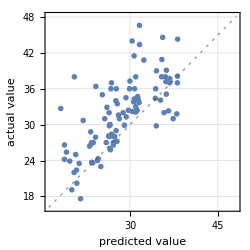
Predictor Measurements
Predictor method | GradientBoostedTrees
Number of test examples | 98
Standard deviation | 5.51 ± 0.48
Standard deviation baseline | 5.94 ± 0.4
R-squared | 0.138 ± 0.19
Mean cross entropy | 3.82 ± 0.32
Single evaluation time | 6.06 ms/example
Batch evaluation speed | 641. examples/s
-Graphics- |

```mathematica
pm = PredictorMeasurements[p,testing]
```

预测器的评估矩阵

```mathematica
pm["Report"]
```

Predictor Measurements
Predictor method | GradientBoostedTrees
Number of test examples | 98
Standard deviation | 5.51 ± 0.48
Standard deviation baseline | 5.94 ± 0.4
R-squared | 0.138 ± 0.19
Mean cross entropy | 3.82 ± 0.32
Single evaluation time | 6.06 ms/example
Batch evaluation speed | 641. examples/s
-Graphics- |

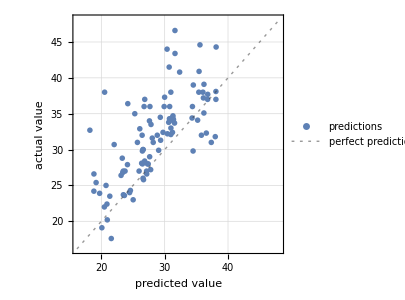
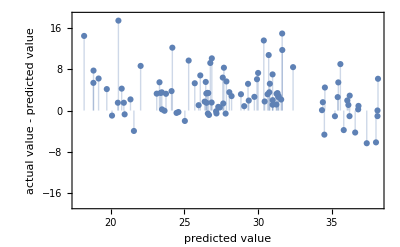
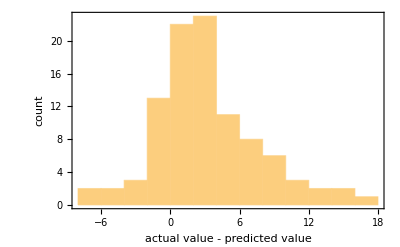

```mathematica
pm[{"ComparisonPlot","ResidualPlot","ResidualHistogram"}]//Column
```

### 其他输入数据类型

训练预测器预测图像的着色面积：

```mathematica
p=Predict[{-Graphics- -> 40.2, -Graphics- -> 8.9, -Graphics- -> 11., -Graphics- -> 4.9, -Graphics- -> 13.6, -Graphics- -> 15.6, -Graphics- -> 14.7, -Graphics- -> 3.8, -Graphics- -> 34.7, -Graphics- -> 10.8, -Graphics- -> 4., -Graphics- -> 16.1, -Graphics- -> 3.3, -Graphics- -> 8.3, -Graphics- -> 12.6}]
```

PredictorFunction[…]

```mathematica
p[{-Graphics-, -Graphics-, -Graphics-}]
```

{9.73333,9.73333,9.73333}

用日期数据类型进行训练

```mathematica
data={DateObject[{2014,5,5,9,53,6.301578998565674},"Instant","Gregorian",-5.]->1,DateObject[{2000,1,1,0,0,0.},"Instant","Gregorian",-5.]->2,DateObject[{2007,8,23},"Day","Gregorian",-6.]->3,DateObject[{2016,4,4,15,59,18.273754119873047},"Instant","Gregorian",-4.]->4};
```

```mathematica
p=Predict[data,FeatureExtractor->({AbsoluteTime[#],#["Year"]}&)]
```

PredictorFunction[…]

```mathematica
p@DateObject[{2017,1,18,23,24,10.098992824554443},"Instant","Gregorian",-5.]
```

2.5

也可指明做归一化处理

```mathematica
p=Predict[data,FeatureExtractor->{{AbsoluteTime[#],#["Year"]}&,"StandardizedVector"}]
```

PredictorFunction[…]

```mathematica
p@DateObject[{2017,1,18,23,24,10.098992824554443},"Instant","Gregorian",-5.]
```

2.5

### 指定算法和参数

鼠标移到 Method 位置显示算法的详细信息

```mathematica
Information[p]
```

Predictor information
Data type | Mixed (number: 8)
Standard deviation | 2.6 ± 0.59
Method | GradientBoostedTrees
Single evaluation time | 5.37 ms/example
Batch evaluation speed | 13.9 examples/ms
Loss | 3.38 ± 0.017
Model memory | 540. kB
Training examples used | 300 examples
Training time | 5.21 s
 |

也可以将参数信息打印出来

```mathematica
Information[p,"MethodOption"]
```

Method→{GradientBoostedTrees,BoostingMethod→Gradient,MaxTrainingRounds→50,LeavesNumber→110,LearningRate→0.2,MaxDepth→6,LeafSize→15,L1Regularization→0,L2Regularization→0}

改变算法和相应参数

```mathematica
p = Predict[training,Method -> {"RandomForest","FeatureFraction"->1/2,"LeafSize"->12}]
```

PredictorFunction[…]

重新测试

```mathematica
pm = PredictorMeasurements[p,testing]
```

性能报告

```mathematica
pm["ComparisonPlot"]
```

### 指明特征的类型

特征数据类型的详细信息

```mathematica
Information[p, FeatureTypes]
```

<|f1→Numerical,f2→Numerical,f3→Numerical,f4→Numerical,f5→Numerical,f6→Numerical,f7→Nominal,f8→Text|>

自定义预测器如何判断特征的类型或者属性

```mathematica
pWithF = Predict[training,FeatureTypes->{"Nominal","Numerical","Numerical","Numerical","Numerical","Nominal","Nominal","Text"}]
```

PredictorFunction[…]

检查所有的特征属性是否和我们指定的一致

```mathematica
Information[pWithF, FeatureTypes]
```

<|f1→Nominal,f2→Numerical,f3→Numerical,f4→Numerical,f5→Numerical,f6→Nominal,f7→Nominal,f8→Text|>

在测试集上进一步检验

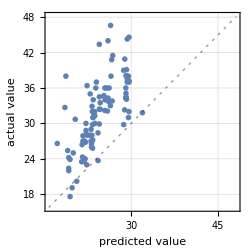
Predictor Measurements
Predictor method | GradientBoostedTrees
Number of test examples | 98
Standard deviation | 8.46 ± 0.49
Standard deviation baseline | 5.94 ± 0.4
R-squared | -1.03 ± 0.36
Mean cross entropy | 4.31 ± 0.0051
Single evaluation time | 5.83 ms/example
Batch evaluation speed | 1.7 examples/ms
-Graphics- |

```mathematica
pmWithF = PredictorMeasurements[pWithF,testing]
```

预测器性能报告

```mathematica
pmWithF["Report"]
```

Predictor Measurements
Predictor method | GradientBoostedTrees
Number of test examples | 98
Standard deviation | 8.46 ± 0.49
Standard deviation baseline | 5.94 ± 0.4
R-squared | -1.03 ± 0.36
Mean cross entropy | 4.31 ± 0.0051
Single evaluation time | 5.83 ms/example
Batch evaluation speed | 1.7 examples/ms
-Graphics- |

## 定制预测器

### 预测器可用算法

通过改变 Method 选项更换算法

DecisionTree

GradientBoostedTrees

LinearRegression

NearestNeighbors

NeuralNetwork

RandomForest

GaussianProcess

产生一些训练数据

```mathematica
data=Table[n->Sin[n],{n,1,10}]
```

用随机森林来训练

```mathematica
randomforest = Predict[data,Method-> "RandomForest"]
```

用 Gaussian Process 来训练

```mathematica
gaussianprocess= Predict[data,Method-> "GaussianProcess"]
```

比较两种方法得结果

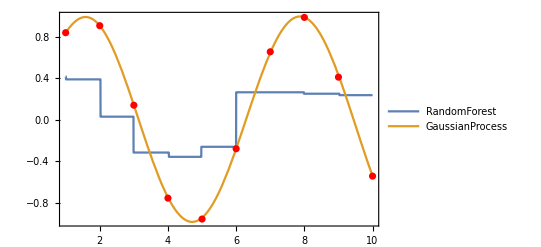

```mathematica
Plot[{randomforest[x], gaussianprocess[x]}, {x,0,10},Exclusions->None,Epilog->{PointSize[Medium],Red, Point[{#,Sin[#]}]&/@Range[10]},PlotLegends->{"RandomForest","GaussianExpress"}]
```

比较两种训练方法的差异

```mathematica
(Information[#1,"TrainingTime"]&)/@{randomforest,gaussianprocess}
```

### 性能目标

针对 TrainingSpeed 优化

```mathematica
p1=Predict[data,PerformanceGoal->"TrainingSpeed"]
```

针对 Quality 优化

```mathematica
p2=Predict[data,PerformanceGoal->"Quality"]
```

比较两种训练方式的耗时

```mathematica
(Information[#1,"TrainingTime"]&)/@{p1,p2}
```

检查缺省情况下的预测器训练耗时

```mathematica
p3=Predict[data]
```

```mathematica
Information[p3,"TrainingTime"]
```

## 序列预测

SequencePredict 函数用来预测离散数列的下一项

产生 SequencePredictorFunction:

```mathematica
spf=SequencePredict[{{1,2,3,4,1,2,3,4,1,2,3,4,1,2,3,4,1,2,3,4}}]
```

SequencePredictorFunction[…]

用序列预测器产生给定数列的第三项

```mathematica
spf[{1,2}]
```

3

### 示例: 像莎士比亚一样写作

SequencePredict 函数可以用来训练并且产生一个类似莎士比亚写作风格的词序列

选取莎士比亚的一些著作

```mathematica
Othello=Import["http://www.gutenberg.org/cache/epub/2267/pg2267.txt"];
Hamlet=Import["http://www.gutenberg.org/cache/epub/2265/pg2265.txt"];
Macbeth=Import["http://www.gutenberg.org/cache/epub/2264/pg2264.txt"];
```

把三个著作联合起来变成一个长篇

```mathematica
shakespearesWorks = StringJoin[Othello," ",Hamlet, " ", Macbeth];
```

训练序列预测器

```mathematica
spchar=SequencePredict[{shakespearesWorks}]
```

在莎士比亚风格的字符序列中随机取样

```mathematica
spchar[{"I"},"RandomNextElement"->100]
```

训练另外一个序列。其中我们把字符串看成词，而不是简单的字符数组

```mathematica
spword=SequencePredict[{shakespearesWorks},FeatureExtractor->"SegmentedWords"]
```

产生50个连续词组，并连成句子

```mathematica
spword["I","RandomNextElement"->100]
```

更换马克洛夫模型的阶并且重新训练

```mathematica
spword=SequencePredict[{shakespearesWorks},FeatureExtractor->"SegmentedWords",Method->{"Markov","Order"->5}];spword["I","RandomNextElement"->100]
```

## 进阶处理技巧

### 不平衡的输入数据

比方说数据在某些分类中的出现频率更高，或者比重更大

例如和男性相关数据远多于女性相关数据

```mathematica
cf=Classify[{1.82->"male",1.90->"male",1.75->"male",1.55->"male",1.6->"female"}]
```

ClassifierFunction[…]

以下更为合理的输出应为女性

```mathematica
cf[1.6]
```

male

当特征从1到2变换的时候，输出为女性的概率

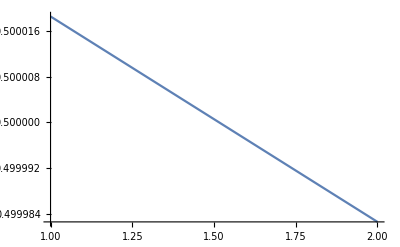

```mathematica
Plot[cf[x,{"Probability","female"}],{x,1,2}]
```

给定特征输入，两个被标记的类的各自的概率

```mathematica
cf[1.6,"Probabilities"]
```

<|female→0.499997,male→0.500003|>

通过 ClassPriors 加入显式先验条件（独立于任何已经给定的训练数据）

```mathematica
cf[1.6,"Probabilities",ClassPriors-><|"male"->0.5,"female"->0.5|>]
```

<|female→0.714283,male→0.285717|>

### 不平衡的输出问题

一些情况下最可能的输出不一定是最好的输出

设置一个合理平衡的培训集，包括来自健康和疾病分类的样本

```mathematica
trainingset = {1->"healthy",2->"diseased",3->"healthy",4->"diseased",5->"diseased"};
```

训练分类器

```mathematica
c=Classify[trainingset]
```

ClassifierFunction[…]

对于一个新示例，预测最有可能的类

```mathematica
c[1.5, "Probabilities"]
```

<|diseased→0.499995,healthy→0.500005|>

```mathematica
c[1.5]
```

healthy

设置决定效用，以惩罚对“diseased”的误分类:

```mathematica
c[2.5,UtilityFunction-> <|"healthy"-> <|"healthy"-> 1, "diseased"-> 0|>,"diseased"-> <|"healthy"-> -1,"diseased"->1|>|>]
```

diseased

### 示例: 可食用蘑菇和有毒蘑菇的分类

在根据某些特征将蘑菇归类为”有毒”和”可食用”的示例任务中，可以探讨效用值和类优先级的有用性.

导入蘑菇种类的训练集和测试集数据

```mathematica
trainingset = ExampleData[{"MachineLearning","Mushroom"},"TrainingData"];
```

```mathematica
testset = ExampleData[{"MachineLearning","Mushroom"},"TestData"];
```

在部分训练集数据上训练分类器

```mathematica
c=Classify[RandomSample[trainingset,100]]
```

ClassifierFunction[…]

在测试数据上的混淆矩阵

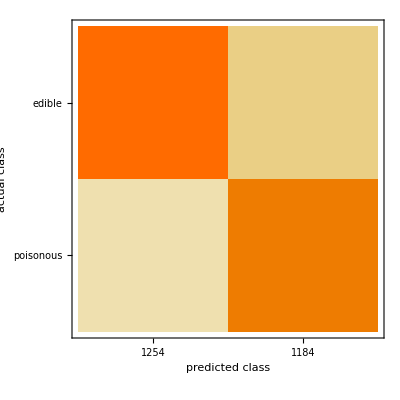

```mathematica
ClassifierMeasurements[c,testset,"ConfusionMatrixPlot"]
```

通过 ClassPriors 设定与数据集无关的先验概率

假设可食用蘑菇占总蘑菇种类中的75%

```mathematica
priors = <|"edible"->0.75,"poisonous"->0.25|>
```

<|edible→0.75,poisonous→0.25|>

UtilityFunction 设定每种判断所对应的效用值

```mathematica
utility = <|
"edible"-><|"edible"-> 1,"poisonous"-> 0,Indeterminate-> 0.5|>,
"poisonous"-><|"edible"-> -10,"poisonous"->1, Indeterminate-> 0.8|>
|>;
```

ClassPriors 设定完成以后，重新考察混淆矩阵

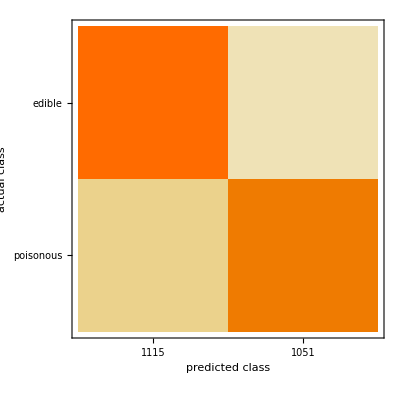

```mathematica
ClassifierMeasurements[c,testset,"ConfusionMatrixPlot",UtilityFunction->utility, ClassPriors->priors]
```

## 学习资源

Elementary Introduction to the Wolfram Language: Chapter 22 | Machine Learning

Wolfram U 视频课程: Learning from Input and Output | Supervised Learning

Wolfram U 视频课程: An Overview of Machine Learning in the Wolfram Language

Wolfram语言最新特性: High-Level Machine Learning

Wolfram语言帮助文档: Machine Learning